Last modified on: Monday, July 9, 2018 at 15:03

Author Info

Rishab Nayak

Garrett Ducharme

Boston University

Poster Session Content

A Performance Analysis of Multiple Neural Networks to Identify Plugs and Connectors from an Image

Analyze the network performance of different Neural Network approaches to solve the same problem: Identify plugs and connectors from its image. This would allow us to understand the implications of using different network frameworks on accuracy and compute time, and understand the tradeoffs.

Add the most representative image of your project here. (We recommend just 1 image, if you add more, we will make a collage of the images.)

-Graphics--Graphics-

On analyzing the data, it was found that the Ademxapp v2 network performed the best, with an accuracy of 91%, but also was one of the slowest networks, having an evaluation time of 1.10s. The fastest network was the ImageIdentify v2 network, with an evaluation time of 0.062s, however, it compromised on accuracy, dropping to 82%. 
From the data collected, it appears that there exists a direct relationship between accuracy and speed for Neural Networks. As the depth of the network increases, the accuracy increases, resulting an increase in evaluation time.

Use a more diverse dataset, recognize more categories of images.
Implement a faster version of the network as an API for use as an app for mobile phones, part of a larger application that provides users with contextual awareness about their environment.

Note: Everything above this bar is your poster.Make sure it fits on a single page. "Preview Poster"

End of School Presentation Content

In addition to the poster content, include other content to present at the 2 minute presentation for end of school. Use the buttons below to add more sections."Add Header""Add Text""Add Code or Image"

Best Performer: Accuracy

The Ademxapp v2 Net trained on a dataset containing a total of 24000 images of 32 Port and connector categories was 91% accurate at classifying

Section Header

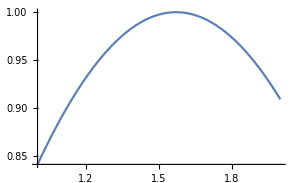
Plot[Sin[x],{x,1,2}]
-Graphics-

Note: Everything above this bar is in your 2 minute presentation. Make sure it fits on 2 slides. "Preview Presentation"

Detailed Project Notes

#### Main Results in Detail

#### Code

##### Data Preparation

Enumerate Recognizable Entities

```mathematica
entityList={"MIDImale","MIDIfemale","RJ45male","RJ45female","TOSLINKmale","TOSLINKfemale","compositevideomalecable","compositevideoport","componentvideocable","componentvideoport","VGAcable","VGAport","dvicable","dviport","minidisplayportcable","minidisplayportport","HDMIcable","HDMIport","DisplayPortcable","DisplayPortport","usbamale","usbafemale","usbcmale","usbcfemale","microusbfemale","microusbmalecable","firewire800cable","firewire800port","firewire400port","firewire400cable","coaxcable","coaxport"};
```

Import Random Backgrounds to use as Underlay

```mathematica
allbackgrounds = Import[StringJoin[NotebookDirectory[],"Backgrounds/",ToString@#,".jpg"]]&/@Range[868];
```

```mathematica
backgrounds = ImageResize[#,{700,700}]&/@allbackgrounds;
```

Process All Images (Resize, Rotate, and use ImageCompose) to Create the Training and Validation Dataset

```mathematica
processAllTraining[foldername_,backgrounds_]:=Block[{inputimages,croppedimages,rotated1,rotated2,rotated3,rotated4, rotated5,rotated6,rotated7,rotated8,rotated9,rotated10,rotated11,rotated12,rotated13,rotated14,rotated15,rotated16,rotatedimages,overlaid,resized,images},
inputimages=Import[StringJoin[NotebookDirectory[],"Images/",foldername,"/",ToString@#,".png"]]&/@Range[50];
croppedimages = ImageCrop[#]&/@inputimages;
images=ImageResize[#,{320,320}]&/@croppedimages;
rotated1=ImageRotate[#,5 Degree]&/@images;
rotated2=ImageRotate[#,-5 Degree]&/@images;
rotated3=ImageRotate[#,10 Degree]&/@images;
rotated4=ImageRotate[#,-10 Degree]&/@images;
rotated5=ImageRotate[#,15 Degree]&/@images;
rotated6=ImageRotate[#,-15 Degree]&/@images;
rotated7=ImageRotate[#,20 Degree]&/@images;
rotated8=ImageRotate[#,-20 Degree]&/@images;
rotated9=ImageRotate[#,25 Degree]&/@images;rotated10=ImageRotate[#,-25 Degree]&/@images;
rotated11=ImageRotate[#,30 Degree]&/@images;rotated12=ImageRotate[#,-30 Degree]&/@images;rotated13=ImageRotate[#,35 Degree]&/@images;rotated14=ImageRotate[#,-35 Degree]&/@images;rotated15=ImageRotate[#,40 Degree]&/@images;rotated16=ImageRotate[#,-40 Degree]&/@images;
rotatedimages = Join[rotated1,rotated2,rotated3,rotated4, rotated5,rotated6,rotated7,rotated8,rotated9,rotated10,rotated11,rotated12,rotated13,rotated14,rotated15,rotated16];
overlaid = ImageCompose[RandomSample[backgrounds,1][[1]],RemoveBackground@#,{{160,160}},{Center,Center}]&/@rotatedimages;
resized = ImageResize[#,{320,320}]&/@overlaid;
Export[StringJoin[NotebookDirectory[],"Images/",foldername,".mx"],#&/@resized];
Print[foldername];
];
```

```mathematica
processAllTraining[#,backgrounds]&/@entityList;
```

Validation Set is Independent of the Training Set to Improve Accuracy

```mathematica
processAllValidation[foldername_,backgrounds_]:=Block[{inputimages,croppedimages,overlaid,resized,images,validation},
inputimages=Import[StringJoin[NotebookDirectory[],"Images/",foldername,"/",ToString@#,".png"]]&/@Range[50];
croppedimages = ImageCrop[#]&/@inputimages;
images=ImageResize[#,{320,320}]&/@croppedimages;
overlaid = ImageCompose[RandomSample[backgrounds,1][[1]],RemoveBackground@#,{{160,160}},{Center,Center}]&/@images;
resized = ImageResize[#,{320,320}]&/@overlaid;
validation = Join[resized,images];
Export[StringJoin[NotebookDirectory[],"Images/",foldername,"validation",".mx"],#&/@validation];
Print[foldername];
];
```

```mathematica
processAllValidation[#,backgrounds]&/@entityList;
```

Convert List of Images to List of Replacement Rules - Create Database

```mathematica
saveRuleListTraining[foldername_]:=Block[{images},
images=Import[StringJoin[NotebookDirectory[],"Images/",foldername,".mx"]];
Export[StringJoin[NotebookDirectory[],"Images/",foldername,".mx"],Thread[#->foldername]&/@images
];
];
```

```mathematica
saveRuleListTraining[#]&/@entityList;
```

```mathematica
saveRuleListValidation[foldername_]:=Block[{images},
images=Import[StringJoin[NotebookDirectory[],"Images/",foldername,"validation",".mx"]];
Export[StringJoin[NotebookDirectory[],"Images/",foldername,"validation",".mx"],Thread[#->foldername]&/@images
];
];
```

```mathematica
saveRuleListValidation[#]&/@entityList;
```

Join Individual Lists of Replacement Rules to Create a List of All Rules

```mathematica
finalRules[]:=Block[{ruleList,validationrulelist},ruleList=Flatten[Join[Import[FileNames[StringJoin[NotebookDirectory[],"Images/",#,".mx"]][[1]]]&/@entityList]];
validationrulelist = Flatten[Join[Import[FileNames[StringJoin[NotebookDirectory[],"Images/",#,"validation",".mx"]][[1]]]&/@entityList]];
Export[StringJoin[NotebookDirectory[],"Test.mx"],ruleList];
Export[StringJoin[NotebookDirectory[],"Validation.mx"],validationrulelist];
];
```

```mathematica
finalRules[];
```

Randomize Arrangement of Replacement Rules to Ensure Batches Have All Types of Data

```mathematica
trainingset=RandomSample[trainingrules,All];
validationset=RandomSample[validationrules,All];
```

##### Image Classification

Attempt 1: Classifier

```mathematica
classifier = Classify[trainingset,ValidationSet->validationset,PerformanceGoal->"Quality"];
```

```mathematica
ClassifierInformation[classifier]
```

Classifier information
Input type | Image
Number of classes | 32
Method | LogisticRegression
Accuracy | 65.9 % ± 4. %
Loss | 1.18 ± 0.11
Single evaluation time | 91. ms/example
Batch evaluation speed | 11.1 examples/s
Classifier memory | 3.9 MB
Training examples used | 1280 examples
Training time | 2 56
 |

Attempt 2: Neural Networks v1

These Neural Networks were trained using Transfer Learning, using the first few layers of the original network, leaving them unchanged and frozen, adding an ImageAugmentation Layer at the beginning of the Network to further augment the dataset, producing reflected versions of the input images along both the x and y axes, with a probability of 0.5  for both. The Output

Null

Null

Null

Null

Null

Null

Null

##### Neural Networks

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

#### Conclusions in Detail

#### All Visualizations

#### Data Sources Links/References

#### Future Directions

#### Background Info Links/References

#### Keywords

Provide keywords as items

< keyword 1 >

< keyword 2 >

#### Other information